## Section 1

```mathematica
Clear["`*"]
(*g[n_,m_]=m;*)
(*gp[n_,m_]=m*)
constraintEqs={};
For[m=0,m<=6,m++,
AppendTo[constraintEqs,g[0,m]==f[m]]
]
For[m=0,m<=6,m++,
AppendTo[constraintEqs,g[1,m]==f[m]]
]
For[m=0,m<=6,m++,
AppendTo[constraintEqs,g[1,m]==f[m]]
]
For[m=0,m<=2,m++,
AppendTo[constraintEqs,gp[0,m]==fp[m]]
]
For[m=0,m<=3,m++,
AppendTo[constraintEqs,gp[1,m]==fp[m]]
]
For[m=0,m<=4,m++,
AppendTo[constraintEqs,gp[1,m]==fp[m]]
]


constraintEqs
Length[constraintEqs]
```

{g[0,0]==f[0],g[0,1]==f[1],g[0,2]==f[2],g[0,3]==f[3],g[0,4]==f[4],g[0,5]==f[5],g[0,6]==f[6],g[1,0]==f[0],g[1,1]==f[1],g[1,2]==f[2],g[1,3]==f[3],g[1,4]==f[4],g[1,5]==f[5],g[1,6]==f[6],g[1,0]==f[0],g[1,1]==f[1],g[1,2]==f[2],g[1,3]==f[3],g[1,4]==f[4],g[1,5]==f[5],g[1,6]==f[6],gp[0,0]==fp[0],gp[0,1]==fp[1],gp[0,2]==fp[2],gp[1,0]==fp[0],gp[1,1]==fp[1],gp[1,2]==fp[2],gp[1,3]==fp[3],gp[1,0]==fp[0],gp[1,1]==fp[1],gp[1,2]==fp[2],gp[1,3]==fp[3],gp[1,4]==fp[4]}

33

```mathematica
pars={g01,g02,g10,g12,g13,g20,g21,g23,g24};

For[i=0,i<=6,i++,
If[i!=0,
AppendTo[pars,StringJoin[ToString[b0],ToString[i]]]
]]
For[i=0,i<=6,i++,
If[i!=1,
AppendTo[pars,StringJoin[ToString[b1],ToString[i]]]
]]
For[i=0,i<=6,i++,
If[i!=2,
AppendTo[pars,StringJoin[ToString[b2],ToString[i]]]
]]



pars
Length[pars]
```

{g01,g02,g10,g12,g13,g20,g21,g23,g24,b01,b02,b03,b04,b05,b06,b10,b12,b13,b14,b15,b16,b20,b21,b23,b24,b25,b26}

27

## Section 2

```mathematica
Clear["`*"]

integrandα=(4*δ^2+8*δ+4)*k^3*Cos[k]+(8*α*δ^2+16*α*δ+8*α)*k^3*(Cos[k])^2-(8*a1*δ+8*a1)*k^2*Sin[k]*Cos[k];
integranda1=(8*a1)*k*(Sin[k])^2-(4*δ+4)*k^2*Sin[k]-(8*α*δ+8*α)*k^2*Sin[k]*Cos[k];

(*r=1*π;
n=1;
δ=0;*)

r=0.839*π;
n=10;
δ=-0.000233;


pdEpdα=1/r*Integrate[integrandα,{k,0,r}]//FullSimplify;
pdEpda1=1/r*Integrate[integranda1,{k,0,r}]//FullSimplify;

pdEpdα=Integrate[D[(k/r)^n*((1+δ)*k*(1+2*α*Cos[k])-2*a1*Sin[k])^2,α],{k,0,r}];
pdEpda1=Integrate[D[(k/r)^n*((1+δ)*k*(1+2*α*Cos[k])-2*a1*Sin[k])^2,a1],{k,0,r}];


(*pdEpdα=Integrate[D[(k/r)^n*((1+δ)*k*(1+2*α*Cos[k]+2*β*Cos[2*k])-2*a1*Sin[k]+2*a2*Sin[2*k]+2*a3*Sin[3*k])^2,α],{k,0,r}];
pdEpdβ=Integrate[D[(k/r)^n*((1+δ)*k*(1+2*α*Cos[k]+2*β*Cos[2*k])-2*a1*Sin[k]+2*a2*Sin[2*k]+2*a3*Sin[3*k])^2,β],{k,0,r}];
pdEpda1=Integrate[D[(k/r)^n*((1+δ)*k*(1+2*α*Cos[k]+2*β*Cos[2*k])-2*a1*Sin[k]+2*a2*Sin[2*k]+2*a3*Sin[3*k])^2,a1],{k,0,r}];
pdEpda2=Integrate[D[(k/r)^n*((1+δ)*k*(1+2*α*Cos[k]+2*β*Cos[2*k])-2*a1*Sin[k]+2*a2*Sin[2*k]+2*a3*Sin[3*k])^2,a2],{k,0,r}];
pdEpda3=Integrate[D[(k/r)^n*((1+δ)*k*(1+2*α*Cos[k]+2*β*Cos[2*k])-2*a1*Sin[k]+2*a2*Sin[2*k]+2*a3*Sin[3*k])^2,a3],{k,0,r}];*)



eq1=pdEpdα==0;
eq2=pdEpda1==0;
(*eq3=1+2*α==2*a1*)
nontrivial=Solve[{eq1,eq2(*,eq3*)},{a1,α(*,δ*)}][[1]];
a1NT=a1/.nontrivial[[1]]//N
αNT=α/.nontrivial[[2]]//N
(*δNT=δ/.nontrivial[[3]]//N*)

(*eq1=pdEpdα==0;
eq2=pdEpdβ==0;
(*eq3=pdEpda1==0;
eq4=pdEpda2==0;*)
eq3=1+2*α+2*β==2*1*a1+2*2*a2+2*3*a3;
eq4=3*1^2*α+3*2^2*β==2*1^3*a1+2*2^3*a2+2*3^3*a3;
eq5=pdEpda3==0;
nontrivial2=Solve[{eq1,eq2,eq3,eq4,eq5},{α,β,a1,a2,a3}][[1]];
αNT2=α/.nontrivial2[[1]]//N
βNT2=β/.nontrivial2[[2]]//N
a1NT2=a1/.nontrivial2[[3]]//N
a2NT2=a2/.nontrivial2[[4]]//N
a3NT2=a3/.nontrivial2[[5]]//N*)
```

0.708815

0.41425

## Don’t need

```mathematica
α=(-32+8 π^2)/(π^2+π^4)
(*δ=(-24+14 π^2+a1 π^2-2 π^4+a1 π^4)/(2 (12-7 π^2+π^4))*)
a1Eq=(2 (12-7 π^2+π^4+12 δ-7 π^2 δ+π^4 δ))/(π^2 (1+π^2))
Solve[a1Eq==a1,{δ}]
```

(-32+8 π^2)/(π^2+π^4)

(2 (12-7 π^2+π^4+12 δ-7 π^2 δ+π^4 δ))/(π^2 (1+π^2))

{{δ→(a1+14/(1+π^2)-24/(π^2 (1+π^2))-(2 π^2)/(1+π^2))/(-14/(1+π^2)+24/(π^2 (1+π^2))+(2 π^2)/(1+π^2))}}

## Section 3

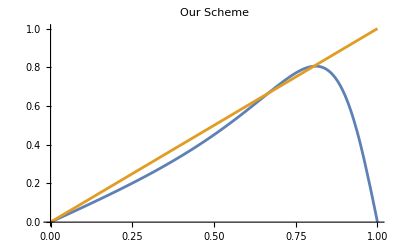

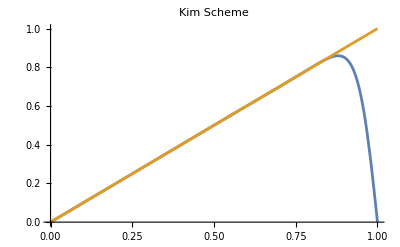

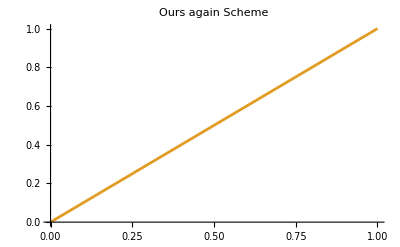

```mathematica
κbarTriTri[κ_]=(2*a1*Sin[κ*π])/(1+2*α*Cos[κ*π]);
αKim=0.5862704032801503;
βKim=0.09549533555017055;
a1Kim=0.6431406736919156;
a2Kim=0.2586011023495066;
a3Kim=0.007140953479797375;
κbarPentHept[κ_]=(2*(a1*Sin[κ*π]+a2*Sin[2*κ*π]+a3*Sin[3*κ*π]))/(1+2*α*Cos[κ*π]+2*β*Cos[2*κ*π]);
Plot[{κbarTriTri[κ]/π/.{a1->a1NT,α->αNT},κ},{κ,0,1},PlotRange->{0,1},PlotLabel->"Our Scheme"]
Plot[{κbarPentHept[κ]/π/.{α->αKim,β->βKim,a1->a1Kim,a2->a2Kim,a3->a3Kim},κ},{κ,0,1},PlotRange->{0,1},PlotLabel->"Kim Scheme"]

Plot[{κbarPentHept[κ]/π/.{α->αNT2,β->βNT2,a1->a1NT2,a2->a2NT2,a3->a3NT2},κ},{κ,0,1},PlotRange->{0,1},PlotLabel->"Ours again Scheme"]
```

## Error Testing

```mathematica
FE[α_,β_]=Integrate[((1-0.000233)κ(1+2α Cos[κ]+2 β Cos[2κ])-2 Sum[Subscript[a, m] Sin[m κ],{m,1,3}])^2(κ/2.672)^10,{κ,0,2.672}];
```

```mathematica
FE[α,β]
```

0.0000539058 (27210.-84716.4 α+67661.8 α^2+26483.8 β-49982.3 α β+18021.3 β^2+7331.71 a_1^2+14977.1 a_2^2+a_2 (40038.-61909.6 α+17795.4 β-25578.5 a_3)-34874.6 a_3+57833.4 α a_3-25546.3 β a_3+13212. a_3^2+a_1 (-27034.9+40038. α-7839.74 β-20221.2 a_2+15290.8 a_3))

```mathematica
rules=Solve[{1+2(α+β)==2 Sum[Subscript[a, m] m,{m,1,3}],3(α+4β)== Sum[Subscript[a, m] m^3,{m,1,3}],D[FE[α,β],α]==0,D[FE[α,β],β]==0,D[FE[α,β],Subscript[a, 3]]==0},{α,β,Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]//FullSimplify
```

{{α→0.58627,β→0.0954953,a_1→0.643141,a_2→0.258601,a_3→0.00714095}}

```mathematica
SetPrecision[rules,15]
```

{{α→0.586270407801043,β→0.0954953388531206,a_1→0.643140669510437,a_2→0.25860110741634,a_3→0.00714095410368224}}

```mathematica
FE[α,β]/.rules//FullSimplify
```

{2.35245×10^-8}

```mathematica
vals=Solve[{D[FE[α,β]/.rules,Subscript[a, 2]]==0,D[FE[α,β]/.rules,β]==0,D[FE[α,β]/.rules,Subscript[a, 3]]==0},{Subscript[a, 2],β,Subscript[a, 3]}]
```

{{a_2→0.26004,β→0.0964316,a_3→0.00731668}}

```mathematica
α/.vals[[1]]
β/.vals[[1]]
Subscript[a, 3]/.vals[[1]]
```

0.587826

0.0966301

0.00735334

```mathematica
2.672/π
```

0.850524

```mathematica
0.2600402841316193
```

```mathematica
FE2[α_,β_,r_,n_]=Integrate[((1-0.000233)κ(1+2α Cos[κ]+2 β Cos[2κ])-2 Sum[Subscript[a, m] Sin[m κ],{m,1,3}])^2(κ/r)^n,{κ,0,r}];
FE2[α,β,π,1]
```

7.74796-22.4098 α+20.2061 α^2+9.42039 β-26.4081 α β+16.6735 β^2-7.47167 a_1+6.28172 α a_1+3.47244 β a_1-((-1-2 π^2 BesselJ[-3/2,2 π]-2 π^3 BesselJ[-1/2,2 π]) a_1^2)/(2 π)+6.28172 a_2-11.4709 α a_2+3.14086 β a_2+2 π (-16/(9 π^2)-√2 BesselJ[-3/2,π]+√(2/3) BesselJ[-3/2,3 π]) a_1 a_2-((-1-4 √2 π^2 BesselJ[-3/2,4 π]-8 √2 π^3 BesselJ[-1/2,4 π]) a_2^2)/(8 π)-3.99923 a_3+9.42258 α a_3-9.94363 β a_3+2 π (-3/(8 π^2)-BesselJ[-3/2,2 π]+BesselJ[-3/2,4 π]/(√2)) a_1 a_3+2 π (-48/(25 π^2)-√2 BesselJ[-3/2,π]+√(2/5) BesselJ[-3/2,5 π]) a_2 a_3-((-1-6 √3 π^2 BesselJ[-3/2,6 π]-18 √3 π^3 BesselJ[-1/2,6 π]) a_3^2)/(18 π)

```mathematica
((1-δ)κ(1+2α Cos[κ])-2 a1 Sin[1 κ])^2(κ)^1//Expand
```

κ^3-2 δ κ^3+δ^2 κ^3+4 α κ^3 Cos[κ]-8 α δ κ^3 Cos[κ]+4 α δ^2 κ^3 Cos[κ]+4 α^2 κ^3 Cos[κ]^2-8 α^2 δ κ^3 Cos[κ]^2+4 α^2 δ^2 κ^3 Cos[κ]^2-4 a1 κ^2 Sin[κ]+4 a1 δ κ^2 Sin[κ]-8 a1 α κ^2 Cos[κ] Sin[κ]+8 a1 α δ κ^2 Cos[κ] Sin[κ]+4 a1^2 κ Sin[κ]^2